## preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

tmp

## temp

### Definition / Theorem

#### Example

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes CAN

Complex Integration

## Contour Integral

### Definition / Theorem

#### Example

```mathematica
cContourIntegral[1/z,z,cPath[4]]//Expand
```

2 ⅈ π

## tmp

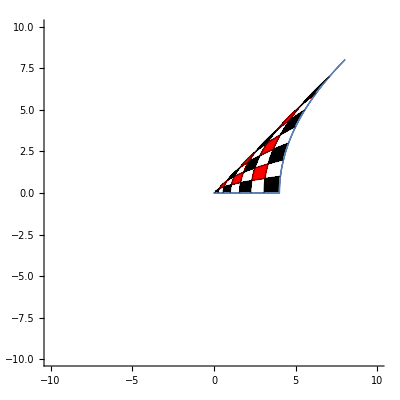

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[{σ^2+t^2,2σ t},{σ,0,2},{t,0,2},
Frame->False,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-10,10},{-10,10}}]
]&/@{Identity}]
```

```mathematica
(z-I Im[z])^2-(-I z+ I Re[z])^2+2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify
```

z^2

```mathematica
((z-I Im[z])^2+(-I z+ I Re[z])^2+2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify)/.z:>"#"
```

1/2 (#^2+2 # Conjugate[#]-Conjugate[#]^2)

```mathematica
(z-I Im[z])^2-(-I z+ I Re[z])^2-2I (z-I Im[z])(-I z+ I Re[z])//FullSimplify
```

Conjugate[z]^2

```mathematica
D[ComplexExpand[Re[(x+I y)^2]],{x,1}]
D[ComplexExpand[Im[(x+I y)^2]],{y,1}]
D[ComplexExpand[Re[(x+I y)^2]],{y,1}]
-D[ComplexExpand[Im[(x+I y)^2]],{x,1}]
```

2 x

2 x

-2 y

-2 y

```mathematica
D[ComplexExpand[Re[Conjugate[(x+I y)]^2]],{x,1}]
D[ComplexExpand[Im[Conjugate[(x+I y)]^2]],{y,1}]
D[ComplexExpand[Re[Conjugate[(x+I y)]^2]],{y,1}]
-D[ComplexExpand[Im[Conjugate[(x+I y)]^2]],{x,1}]
```

2 x

-2 x

-2 y

2 y

Visualizations

## Visualize Function

## Test-0

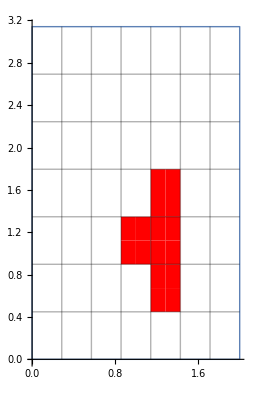

```mathematica
ClearAll[t1,t2,r1,r2,dt,dr]
F[z_]:=Gamma[z]
F[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
r1=0;
r2=2;
t1=0;
t2=Pi;
GraphicsRow[
With[{z=r + I t,col=Red},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->6,
MeshShading->ArrayPad[{{None,col},{col,col},{None,col}},{{1,5},{3,5}},None],
Frame->False,
AxesOrigin->{0,0}]]&/@{Identity,F}]
```

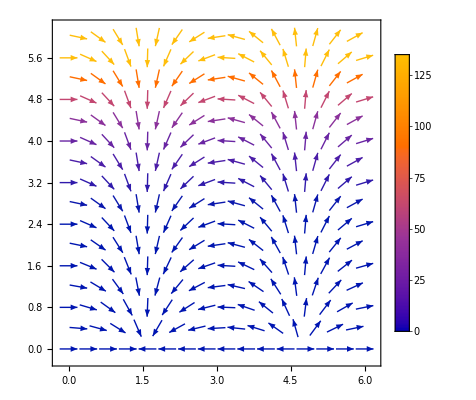

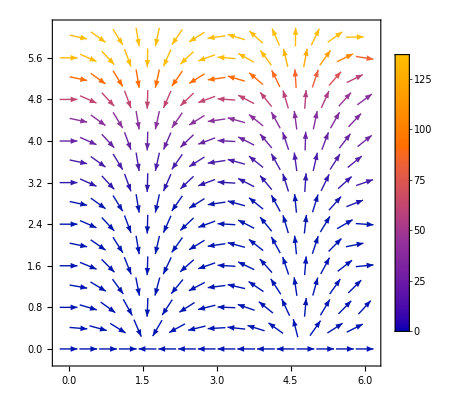

```mathematica
ComplexVectorPlot[Cos[z],{z,0,6+6I},PlotLegends->Automatic]
ComplexVectorPlot[Series[Cos[z],{z,0,12}]//Normal,{z,0,6+6I},PlotLegends->Automatic]
```

## Test-1

```mathematica
f[s_]:=2s
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{x,0,4},{y,0,8}]
]&/@{Identity,f}]
```

-Graphics-

## Test-2

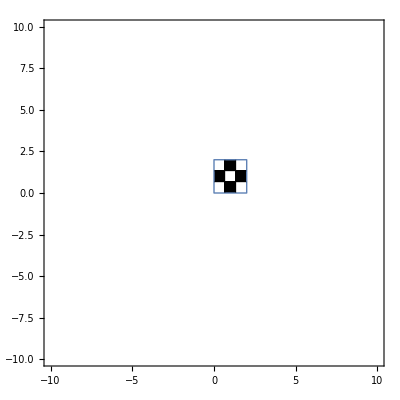

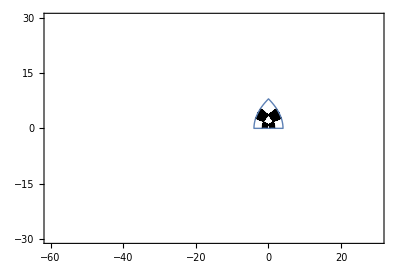

```mathematica
With[{s=σ+I t},
ParametricPlot[ReIm[s],{σ,0,2},{t,0,2},
Mesh->{2,2},
MeshShading->ArrayPad[{{None,Black},{Black,None}},{{0,0},{0,0}},None],
PlotRange->{{-10,10},{-10,10}}]
]
With[{s=σ+I t},
ParametricPlot[ReIm[s^2],{σ,0,2},{t,0,2},
Mesh->{2,2},
MeshShading->ArrayPad[{{None,Black},{Black,None}},{{0,0},{0,0}},None],
PlotRange->{{-60,30},{-30,30}}]
]
```

## Test-3

### Demo-1

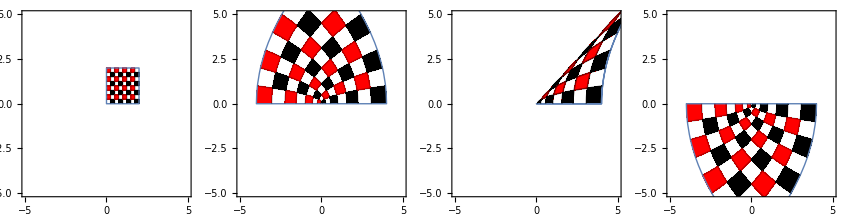

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,2},{t,0,2},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,#^2&,1/2 (#^2+2 # Conjugate[#]-Conjugate[#]^2)&,Conjugate[#]^2&}]
```

### Demo-2

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,{0,1}]&,WeierstrassP[#,{1,0}]&}]
```

### Problem-1: Weierstrass-p is an even function : How to explain the following graphs below

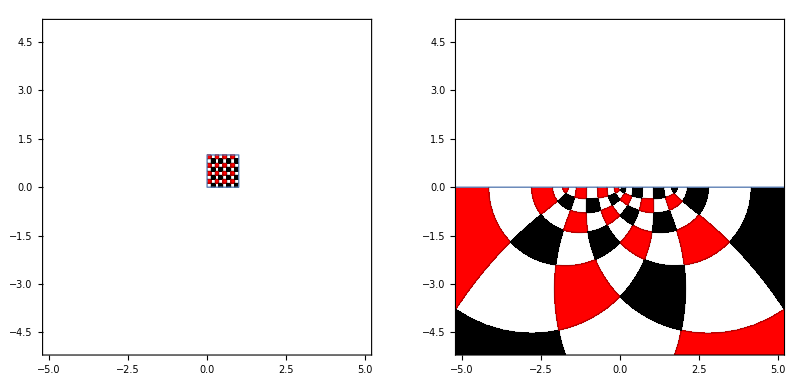

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

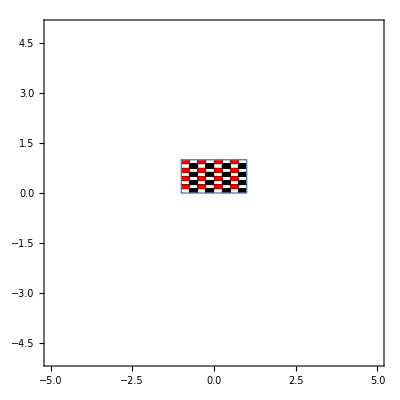

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,-1,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

```mathematica
ComplexPlot3D[WeierstrassP[z,WeierstrassInvariants[{2,2I}]],{z,0,10+10I},PlotLegends->Automatic]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

-Graphics3D-

```mathematica
WeierstrassInvariants[{1,I}]//N
```

{11.817+0. ⅈ,2.15808×10^-15+0. ⅈ}

### Demo-3

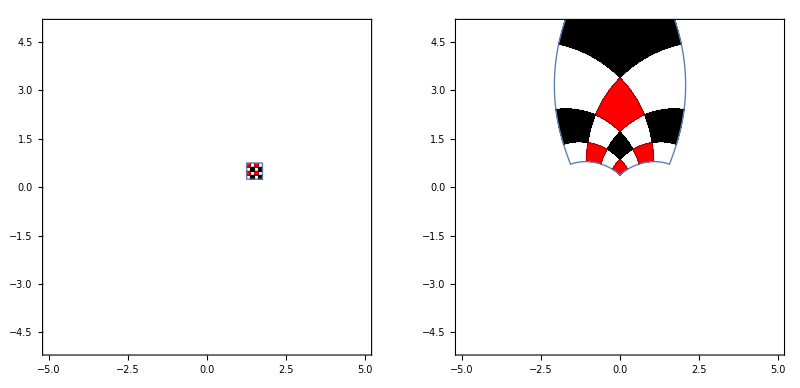

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,1.25,1.75},{t,0.25,0.75},
Axes->{True,True},
Frame->True,
Mesh->{3,3},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]&}]
```

### tmp

```mathematica
{Identity,#^2&,Gamma[#]&,PolyGamma[0,#]&,Log[#]&}
```

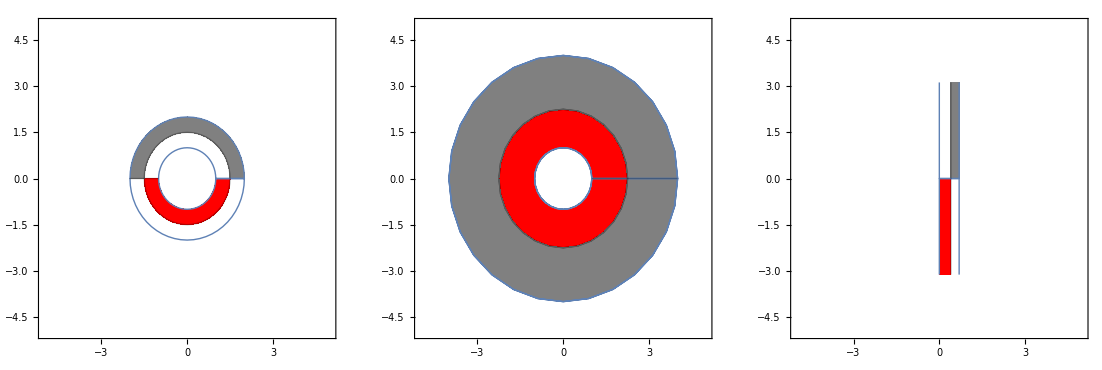

```mathematica
GraphicsRow[
With[{s=r Exp[I t]},
ParametricPlot[ReIm@#[s],{r,1,2},{t,0, 4π/2},
Axes->{True,True},
Frame->True,
Mesh->{1,1},
MeshShading->ArrayPad[{{None,Gray},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-5,5},{-5,5}}]
]&/@{Identity,#^2&,Log[#]&}]
```

### tmp-1

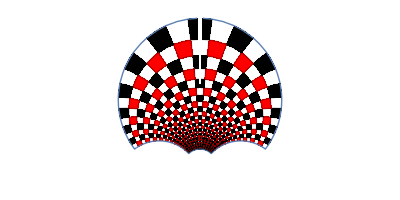

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,-2,2},{t,1,5},
Axes->{False,False},
Frame->False,
Mesh->{26,26},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-1,1},{0,1}}]
]&/@{-1/#&}]
```

```mathematica
{Identity,WeierstrassP[#,WeierstrassInvariants[{1,I}]]+I&,-1/(WeierstrassP[#,WeierstrassInvariants[{1,I}]]+I)&}
```

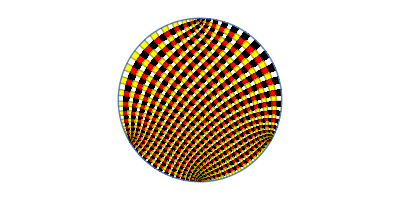

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,1,2},{t,0,1},
Axes->{False,False},
Frame->False,
Mesh->{40,40},
MeshShading->ArrayPad[{{None,Black},{Yellow,Red}},{{0,0},{0,0}},None],
PlotRange->{{-1,1},{0,1}}]
]&/@{-1/(WeierstrassP[#,WeierstrassInvariants[{1,I}]]+I)&}]
```

## Test-4

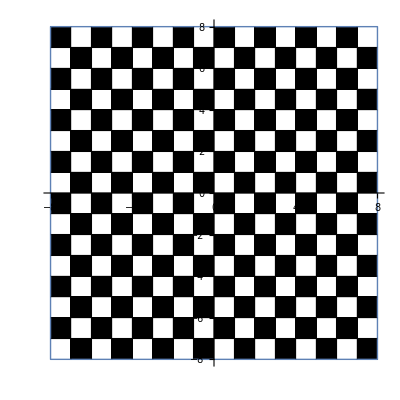

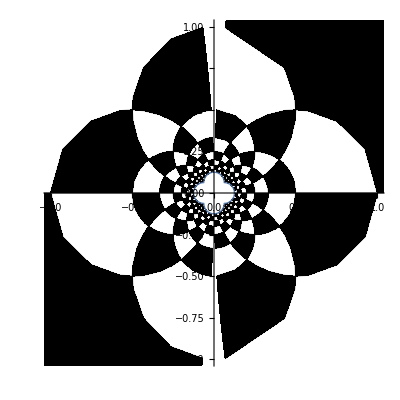

```mathematica
F[z_]:=1/z
r1=-8;
r2=8;
t1=-8;
t2=8;
GraphicsRow[
With[{z=r +I t,col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->15,
MeshShading->{{None,col},{col,None}},
Frame->False,AxesOrigin->{0,0},PlotRange->{{-8,8},{-8,8}}]
]&/@{Identity}]
GraphicsRow[
With[{z=r +I t,col=Black},
ParametricPlot[ReIm@#[z],{r,r1,r2},{t,t1,t2},
Mesh->15,
MeshShading->{{None,col},{col,None}},
Frame->False,AxesOrigin->{0,0},PlotRange->{{-1,1},{-1,1}}]
]&/@{F}]
```

```mathematica
|
```

```mathematica
√(1+I)//N
```

1.09868+0.45509 ⅈ

```mathematica
(-1.0986841134678098-0.45508986056222733 ⅈ)^2
```

1.+1. ⅈ

```mathematica
(-1.0986841134678098-0.45508986056222733 ⅈ)^2
```

1.+1. ⅈ

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m"]
rsurf[func_]:=Grid[{
{RiemannSurfacePlot3D[w==func,Re[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Im[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False],RiemannSurfacePlot3D[w==func,Im[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Re[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False]}}];
```

```mathematica
rsurf/@{Log[z]}
```

{-Graphics3D- | -Graphics3D-}

```mathematica
Series[Cos[z],{z,0,12}]//Normal
```

1-z^2/2+z^4/24-z^6/720+z^8/40320-z^10/3628800+z^12/479001600